```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY193_cloudy/sec_int_data/675nm.dat"]
```

{{1.46129,0.126016},{1.36603,0.161353},{1.32759,0.171682},{1.2815,0.177644},{1.23231,0.188386},{1.21009,0.189545},{1.18279,0.168476},{1.15809,0.103278},{1.13892,0.0391246},{1.12738,0.00727348},{1.09219,0.0589291},{1.09146,0.129448},{1.09503,0.222583},{1.10053,0.231905},{1.1079,0.229682},{1.12128,0.232698},{1.13179,0.214385},{1.14273,0.225301},{1.16583,0.220901},{1.1846,0.215353},{1.20387,0.254875},{1.22314,0.226897},{1.24682,0.216481}}

0.164277+0.00853686 x

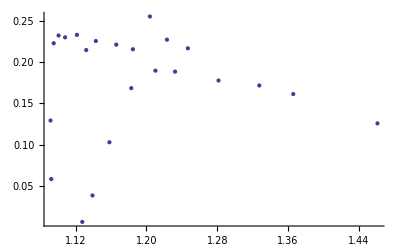

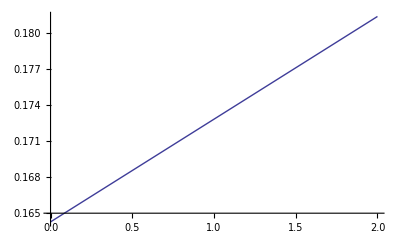

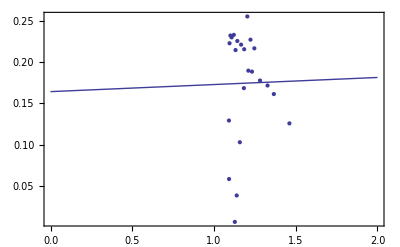

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```